## Introduced Top Predator (P): suboptimal defense toward P

Define Model

```mathematica
(* Modeling suboptimal defense -- Introduce ϕ the ratio of effeciency of introduced predator to recognized predator. As, ϕ goes to 1 defense against introduced pred is equally efficient. As it goes to zero defense effectiveness decreases. As efficiency shows up in the cost equations suboptimal response penalizes with NCEs as well  *)
```

```mathematica
Clear["Global`*"]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fΝ (1-ϕ)));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fΝ (1-ϕ)) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(*fitness is defined as the per capita growth rate of the resource*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fΝ) -  aPR P (1 - eP fΝ (1-ϕ));
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
```

eΝ v (c0 (-1+eP+eΝ) r-aΝR (-1+eΝ) fΝ Ν+aPR eP fΝ P (-1+ϕ))

eP v (c0 (-1+eP+eΝ) r-aΝR eΝ fΝ Ν+aPR (-1+eP) fΝ P (-1+ϕ))

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1,k-> 6, c0->0.2, fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->1};
parsM = {r-> 1,k-> 6, c0->0.2, fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->.75};
parsL = {r-> 1,k-> 6, c0->0.2, fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->.5};
parsCoexH = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1}
parsCoexM = {r-> 1,k-> 6, c0->0.2, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->.75}
parsCoexL = {r-> 1,k-> 6, c0->0.2, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->.5}
```

{r→1,k→5,c0→0.25,fΝ→0.8,aPR→0.9,aPΝ→1.2,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.2,v→1,ϕ→1}

{r→1,k→6,c0→0.2,fΝ→0.8,aPR→0.9,aPΝ→1.2,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.2,v→1,ϕ→0.75}

{r→1,k→6,c0→0.2,fΝ→0.8,aPR→0.9,aPΝ→1.2,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.2,v→1,ϕ→0.5}

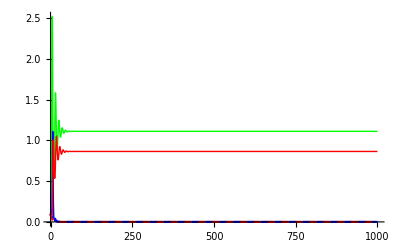

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsCoexH},{R,Ν, P, eΝ, eP},{t,0,1000}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,1000}, PlotStyle-> cols]
```

### Manipulate across gradients ϕ

```mathematica
parsϕman = Delete[parsCoexH, 14];
c0parsRN ={r-> 1,k-> 1, fΝ->0.5,  aPR-> 0.1, aPΝ -> 0.1, aΝR -> 0.8, bPΝ->0.1, bΝR->0.8, bPR->0.1, mP->0.5, mΝ->0.2, v-> 1, ϕ->1}
```

{r→1,k→1,fΝ→0.5,aPR→0.1,aPΝ→0.1,aΝR→0.8,bPΝ→0.1,bΝR→0.8,bPR→0.1,mP→0.5,mΝ→0.2,v→1,ϕ→1}

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[c0parsRN,{c0 -> χ}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{χ,0.5,"c0"},0,1}]
```

Simulation plots

### Final densities of RNP across relative efficiencies of toward P (ϕ)

```mathematica
parsaltϕ = {r-> 0.9,k-> 5, c0->0.1, fΝ->0.7,  fP->0.7,aPR-> 0.5, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.6, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.25, v-> 1};
```

```mathematica
parsϕ = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1}
```

{r→1,k→5,c0→0.25,fΝ→0.8,aPR→0.9,aPΝ→1.2,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.2,v→1}

```mathematica
finalϕ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsaltϕ},{R,Ν, P, eΝ, eP},{t,0,500}, {ϕ}];
finalϕR = Plot[Evaluate[R[ϕ][500]/.finalϕ,{ϕ,1,0}],PlotStyle-> {Thickness[0.015], Green} ,
PlotRange->{{1,0},{0,3}}];
finalϕΝ = Plot[Evaluate[Ν[ϕ][500]/.finalϕ,{ϕ,1,0}],PlotStyle-> {Thickness[0.015], Blue}, 
PlotRange->{{1,0},{0,3}}];
finalϕP = Plot[Evaluate[P[ϕ][500]/.finalϕ,{ϕ,1,0}],PlotStyle-> {Thickness[0.015], Red}, 
PlotRange->{{1,0},{0,3}}];
finalϕeΝ = Plot[Evaluate[eΝ[ϕ][500]/.finalϕ,{ϕ,1,0}],PlotStyle-> {Thickness[0.015],Blue, Dashed}, 
PlotRange->{{1,0},{0,3}}];
finalϕeP = Plot[Evaluate[eP[ϕ][500]/.finalϕ,{ϕ,1,0}],PlotStyle-> {Thickness[0.015],Red, Dashed}, 
PlotRange->{{1,0},{0,3}}];
```

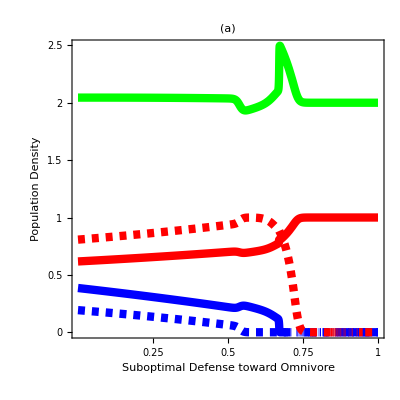

```mathematica
Fig4a = Show[finalϕR,finalϕΝ,finalϕeΝ, finalϕP, finalϕeP,
PlotLabel -> Style["(a)                                                                                       ", FontSize->14,  Bold],
Frame-> True,FrameLabel->{"Suboptimal Defense toward Omnivore","Population Density", None,"Defense Effort"}, Spacings -> 30, 
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, FrameTicks->{{{0,0.5,1, 1.5, 2, 2.5},{0,0.5,1, 1.5, 2, 2.5}},{{1, 0.75, 0.5,0.25}, {None}}}]
```

### Final densities of RNP across productivity gradient for various levels of ϕ

#### Manipulate across gradient of k

```mathematica
kaPNc0ϕpars = Delete[parsCoexH, {{2},{3},{6}, {14}}]
```

{r→1,fΝ→0.8,aPR→0.9,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.2,v→1}

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[kaPNc0ϕpars,{k -> κ, c0 -> χ, aPΝ -> α, ϕ -> Φ}]},
{R,Ν, P, eΝ, eP},{t,0,500}]]],
{t,0,500},PlotRange->{0,All}, PlotStyle->cols],
{{κ,5,"k"},0,10}, {{χ,0.2,"c0"},0,1}, {{α,1.2,"aPΝ"},0,4}, {{Φ,1,"ϕ"},0,1}]
```

```mathematica
kparsϕH = {r-> 1, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
kparsϕM = {r-> 1, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->0.75};
kparsϕL = {r-> 1, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->0.5};
```

```mathematica
kfinalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsϕH},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsϕM },{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
kfinalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsϕL},{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
```

```mathematica
kfinalRH = Plot[Evaluate[R[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝH = Plot[Evaluate[Ν[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPH = Plot[Evaluate[P[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

```mathematica
kfinalRM = Plot[Evaluate[R[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝM = Plot[Evaluate[Ν[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPM = Plot[Evaluate[P[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

```mathematica
kfinalRL = Plot[Evaluate[R[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝL  = Plot[Evaluate[Ν[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPL  = Plot[Evaluate[P[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

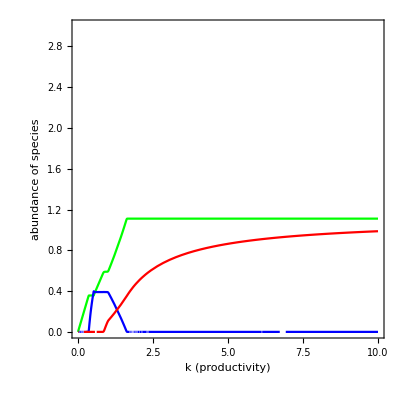

```mathematica
Show[kfinalRH,kfinalΝH,kfinalPH,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

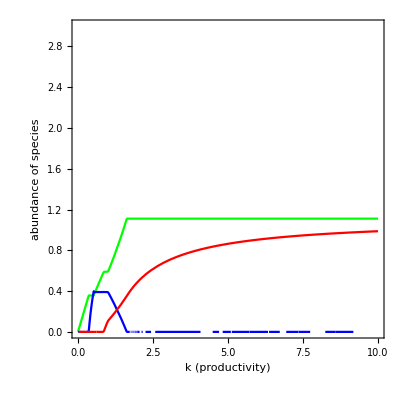

```mathematica
Show[kfinalRM,kfinalΝM, kfinalPM,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1, LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

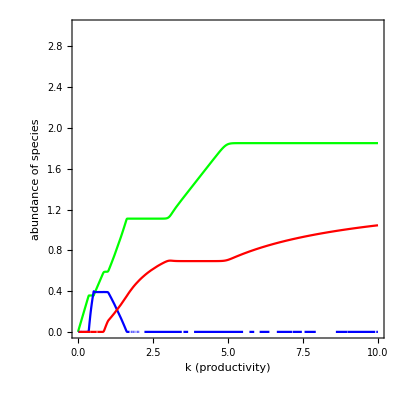

```mathematica
Show[kfinalRL,kfinalΝL,kfinalPL,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

### Plot final densities across a range of c0

```mathematica
c0parsϕH = {r-> 1, k-> 5, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
c0parsϕM = {r-> 1,  k-> 5, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->0.75};
c0parsϕL = {r-> 1, k-> 5, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->0.5};
```

```mathematica
c0finalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕH},{R,Ν, P, eΝ, eP},{t,0,1000}, {c0}];
c0finalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕM },{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
c0finalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕL},{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
```

```mathematica
c0finalRH = Plot[Evaluate[R[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝH = Plot[Evaluate[Ν[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPH = Plot[Evaluate[P[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝH = Plot[Evaluate[eΝ[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePH = Plot[Evaluate[eP[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
c0finalRM = Plot[Evaluate[R[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝM = Plot[Evaluate[Ν[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPM = Plot[Evaluate[P[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝM = Plot[Evaluate[eΝ[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePM = Plot[Evaluate[eP[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
c0finalRL = Plot[Evaluate[R[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝL  = Plot[Evaluate[Ν[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPL  = Plot[Evaluate[P[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝL = Plot[Evaluate[eΝ[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePL = Plot[Evaluate[eP[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

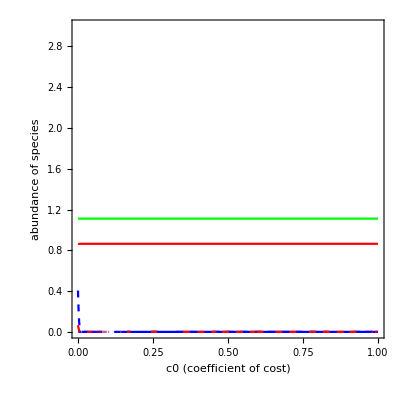

```mathematica
Show[c0finalRH,c0finalΝH,c0finalPH,c0finaleΝH, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

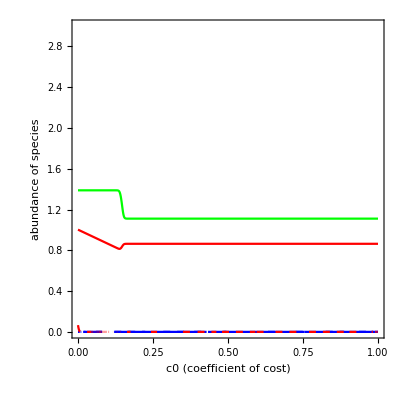

```mathematica
Show[c0finalRM,c0finalΝM,c0finalPM,c0finaleΝM, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

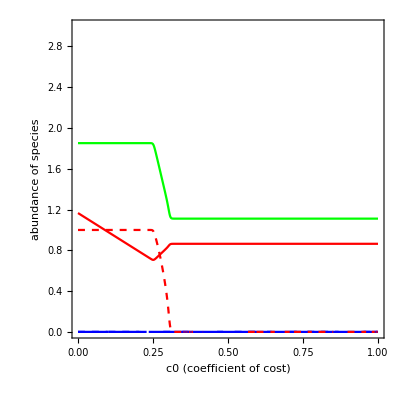

```mathematica
Show[c0finalRL,c0finalΝL,c0finalPL,c0finaleΝL, c0finalePL, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

Solve for equilibria and plot domains of coexistence

### Equilibria

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil//TableForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

R→0 | Ν→0 | P→0 | eΝ→1-eP | 
R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1-eP | 
R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(-mΝ+aΝR bΝR (-1+c0) (-1+fΝ) k r)/(aΝR^2 bΝR (-1+fΝ)^2 k) | P→0 | eΝ→1 | eP→0
R→((-c0+fΝ) k r)/fΝ | Ν→(c0 r)/(aΝR fΝ) | P→0 | eΝ→1/fΝ+mΝ/(aΝR bΝR c0 k r-aΝR bΝR fΝ k r) | eP→0
R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1 | eP→0
R→mP/(aPR bPR) | Ν→0 | P→-(mP+aPR bPR (-1+c0) k r)/(aPR^2 bPR k) | eΝ→1 | eP→0
R→(aΝR fΝ mP-aPΝ bPΝ c0 r)/(aPR aΝR bPR fΝ) | Ν→(c0 r)/(aΝR fΝ) | P→(-aΝR fΝ mP+aPΝ bPΝ c0 r+aPR aΝR bPR (-c0+fΝ) k r)/(aPR^2 aΝR bPR fΝ k) | eΝ→(aΝR fΝ (aPΝ mP+aPR k (aΝR bΝR mP-aPR bPR mΝ))-aPΝ (aPΝ bPΝ c0+aPR aΝR (bPΝ bΝR c0+bPR (-c0+fΝ)) k) r)/(aPR aΝR bΝR fΝ k (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→0
R→(k (aΝR (-1+fΝ) mP+aPR bPΝ mΝ-aPΝ bPΝ (-1+c0) r))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k) | Ν→(-aPR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ)+aPΝ (mP+aPR bPR (-1+c0) k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | P→(-aPΝ bPΝ mΝ+aΝR (-1+fΝ) k (-aΝR bΝR (-1+fΝ) mP-aPR bPR mΝ+aPΝ bPΝ bΝR (-1+c0) r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | eΝ→1 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
R→mP/(aPR bPR) | Ν→0 | P→(-mP/(bPR k)+aPR r)/aPR^2 | eΝ→0 | eP→0
R→(k (-aΝR mP+aPR bPΝ mΝ+aPΝ bPΝ r))/(aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | P→(-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ+aPΝ bPΝ bΝR r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | eΝ→0 | eP→0
R→(k (aΝR mP+aPΝ bPΝ (-1+c0) r+aPR bPΝ mΝ (-1+fΝ-fΝ ϕ)))/(-aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k (1+fΝ (-1+ϕ))) | Ν→(aPΝ (mP+aPR bPR (-1+c0) k r (1+fΝ (-1+ϕ)))-aPR k (-aΝR bΝR mP+aPR bPR mΝ (1+fΝ (-1+ϕ))) (1+fΝ (-1+ϕ)))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k (-1+fΝ-fΝ ϕ))) | P→(-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP-aPΝ bPΝ bΝR (-1+c0) r+aPR bPR mΝ (1+fΝ (-1+ϕ))))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k (-1+fΝ-fΝ ϕ))) | eΝ→0 | eP→1
R→mP/(aPR bPR-aPR bPR fΝ+aPR bPR fΝ ϕ) | Ν→0 | P→-(mP+aPR bPR (-1+c0) k r (1+fΝ (-1+ϕ)))/(bPR k (aPR+aPR fΝ (-1+ϕ))^2) | eΝ→0 | eP→1
R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1+(mP+aPR bPR (-1+c0) k r)/(aPR bPR (-1+c0) fΝ k r (-1+ϕ)) | eP→-(mP+aPR bPR (-1+c0) k r)/(aPR bPR (-1+c0) fΝ k r (-1+ϕ))
R→k r (1+c0/(fΝ (-1+ϕ))) | Ν→0 | P→(c0 r)/(aPR fΝ-aPR fΝ ϕ) | eΝ→0 | eP→1/(fΝ-fΝ ϕ)+mP/(aPR bPR c0 k r-aPR bPR fΝ k r+aPR bPR fΝ k r ϕ)
R→-(k r (fΝ+c0 (-2+ϕ)-fΝ ϕ))/(fΝ (-1+ϕ)) | Ν→(c0 r)/(aΝR fΝ) | P→(c0 r)/(aPR fΝ-aPR fΝ ϕ) | eΝ→(aPΝ c0 r-aPR aΝR bΝR c0 k r (-2+ϕ)-aPR fΝ (mΝ-aΝR bΝR k r) (-1+ϕ))/(aPR aΝR bΝR fΝ k r (-c0 (-2+ϕ)+fΝ (-1+ϕ))) | eP→(aPR aΝR bPR c0 k r (-2+ϕ)-aPΝ bPΝ c0 r (-1+ϕ)+aΝR fΝ (mP-aPR bPR k r) (-1+ϕ))/(aPR aΝR bPR fΝ k r (-c0 (-2+ϕ)+fΝ (-1+ϕ)) (-1+ϕ))
R→(aPR fΝ mΝ+aPΝ c0 r-aPR fΝ mΝ ϕ)/(aPR aΝR bΝR fΝ-aPR aΝR bΝR fΝ ϕ) | Ν→(aPΝ c0 r+aPR aΝR bΝR c0 k r-aPR fΝ (mΝ-aΝR bΝR k r) (-1+ϕ))/(aPR aΝR^2 bΝR fΝ k (-1+ϕ)) | P→(c0 r)/(aPR fΝ-aPR fΝ ϕ) | eΝ→0 | eP→((bΝR (aΝR mP-bPΝ (aPR mΝ+aPΝ r)))/(-aPΝ c0 r+aPR fΝ mΝ (-1+ϕ))-(aPΝ bPΝ-aPR aΝR bPR k+aPR aΝR bPΝ bΝR k)/(aPR aΝR fΝ k-aPR aΝR fΝ k ϕ))/bPR
R→(k (aΝR bΝR mP (2+fΝ (-1+ϕ)-ϕ)-(-1+ϕ) (-aPΝ (bPR-bPΝ bΝR) (-1+c0) r+aPR bPR mΝ (2-fΝ+(-1+fΝ) ϕ))))/(-aPΝ (bPR-bPΝ bΝR) (-1+ϕ)+aPR aΝR bPR bΝR k (-2+fΝ+ϕ-fΝ ϕ)^2) | Ν→((-1+ϕ) (-aPR bPR mΝ (-1+ϕ)+aΝR bΝR (mP+aPR bPR (-1+c0) k r (2-fΝ+(-1+fΝ) ϕ))))/(aΝR (-aPΝ (bPR-bPΝ bΝR) (-1+ϕ)+aPR aΝR bPR bΝR k (-2+fΝ+ϕ-fΝ ϕ)^2)) | P→(aPR bPR mΝ (-1+ϕ)+aΝR bΝR (-mP+aPR bPR (-1+c0) k r (-2+fΝ+ϕ-fΝ ϕ)))/(aPR (-aPΝ (bPR-bPΝ bΝR) (-1+ϕ)+aPR aΝR bPR bΝR k (-2+fΝ+ϕ-fΝ ϕ)^2)) | eΝ→(-aPΝ aΝR (mP+aPR (-1+c0) k r (bPR-bPΝ bΝR (-1+ϕ)+bPR fΝ (-1+ϕ)))+aPR aΝR k (-aΝR bΝR mP+aPR bPR mΝ (1+fΝ (-1+ϕ))) (2+fΝ (-1+ϕ)-ϕ)+aPR aPΝ bPΝ mΝ (-1+ϕ))/(aPR aΝR fΝ k (aΝR bΝR mP (-2+fΝ+ϕ-fΝ ϕ)+(-1+ϕ) (-aPΝ (bPR-bPΝ bΝR) (-1+c0) r+aPR bPR mΝ (2-fΝ+(-1+fΝ) ϕ)))) | eP→(aPΝ (aΝR (mP+aPR (-1+c0) k r (bPR+bPΝ bΝR (-1+fΝ) (-1+ϕ)))-aPR bPΝ mΝ (-1+ϕ))-aPR aΝR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ) (2+fΝ (-1+ϕ)-ϕ))/(aPR aΝR fΝ k (aΝR bΝR mP (-2+fΝ+ϕ-fΝ ϕ)+(-1+ϕ) (-aPΝ (bPR-bPΝ bΝR) (-1+c0) r+aPR bPR mΝ (2-fΝ+(-1+fΝ) ϕ))))
R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR) | Ν→-(mΝ+aΝR bΝR (-1+c0) k r)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | eP→1-1/fΝ+mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)
R→mΝ/(aΝR bΝR) | Ν→(-mΝ/(bΝR k)+aΝR r)/aΝR^2 | P→0 | eΝ→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

```mathematica
(* Only takes a few seconds, just like the Nakazawa formulation (not surprisingly). What is surprising is how much longer the ρ equil takes. I guess that manipulating the replicator equation is qualitatively different than adding a parameter *)
```

```mathematica
thresh19N =equil[[19, 2,2]]
```

(aPΝ c0 r+aPR aΝR bΝR c0 k r-aPR fΝ (mΝ-aΝR bΝR k r) (-1+ϕ))/(aPR aΝR^2 bΝR fΝ k (-1+ϕ))

```mathematica
cost19 =FullSimplify[Solve[thresh19N==0,c0]]
```

{{c0→(aPR fΝ (mΝ-aΝR bΝR k r) (-1+ϕ))/((aPΝ+aPR aΝR bΝR k) r)}}

```mathematica
Νinv9kaPN = plotΝinv9/.c0aPΝparsH;
PlotRP9 = Plot[Νinv9kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,
PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig9RP[x]< 0&&AllFeas9M[x]]];
```

ReplaceAll::reps: {c0aPΝparsH} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
thresh21N =equil[[21, 2,2]]
```

0

```mathematica
thresh21R =equil[[21, 1,2]]
```

0

```mathematica
Solve[thresh21N==0,c0]
```

{{}}

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν-aPR (P+eP fΝ P (-1+ϕ)) | aΝR (-1+eΝ fΝ) R | R (-c0 r+aΝR fΝ Ν) | -aPR R (1+eP fΝ (-1+ϕ)) | R (-c0 r-aPR fΝ P (-1+ϕ))
aΝR bΝR (1-eΝ fΝ) Ν | -mΝ-aPΝ P+aΝR bΝR (1-eΝ fΝ) R | -aΝR bΝR fΝ R Ν | -aPΝ Ν | 0
0 | -aΝR (-1+eΝ) eΝ fΝ v | v (c0 (-1+eP+2 eΝ) r+aΝR (1-2 eΝ) fΝ Ν+aPR eP fΝ P (-1+ϕ)) | aPR eP eΝ fΝ v (-1+ϕ) | eΝ v (c0 r+aPR fΝ P (-1+ϕ))
aPR bPR P (1+eP fΝ (-1+ϕ)) | aPΝ bPΝ P | 0 | -mP+aPΝ bPΝ Ν+aPR bPR R (1+eP fΝ (-1+ϕ)) | aPR bPR fΝ P R (-1+ϕ)
0 | -aΝR eP eΝ fΝ v | eP v (c0 r-aΝR fΝ Ν) | aPR (-1+eP) eP fΝ v (-1+ϕ) | v (c0 (-1+2 eP+eΝ) r-aΝR eΝ fΝ Ν+aPR (-1+2 eP) fΝ P (-1+ϕ)))

(r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν-aPR (P+eP fΝ P (-1+ϕ)) | aΝR (-1+eΝ fΝ) R | R (-c0 r+aΝR fΝ Ν)
aΝR bΝR (1-eΝ fΝ) Ν | -mΝ-aPΝ P+aΝR bΝR (1-eΝ fΝ) R | -aΝR bΝR fΝ R Ν
0 | -aΝR (-1+eΝ) eΝ fΝ v | v (c0 (-1+eP+2 eΝ) r+aΝR (1-2 eΝ) fΝ Ν+aPR eP fΝ P (-1+ϕ)))

(r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν-aPR (P+eP fΝ P (-1+ϕ)) | -aPR R (1+eP fΝ (-1+ϕ)) | R (-c0 r-aPR fΝ P (-1+ϕ))
aPR bPR P (1+eP fΝ (-1+ϕ)) | -mP+aPΝ bPΝ Ν+aPR bPR R (1+eP fΝ (-1+ϕ)) | aPR bPR fΝ P R (-1+ϕ)
0 | aPR (-1+eP) eP fΝ v (-1+ϕ) | v (c0 (-1+2 eP+eΝ) r-aΝR eΝ fΝ Ν+aPR (-1+2 eP) fΝ P (-1+ϕ)))

## Plot cost against IGP strength

### Functions for working with equilibrium values across a gradient of productivity (c0)

```mathematica
subpars=Delete[parsCoexH,3]
subparsM=Delete[parsCoexM,3];
subparsL=Delete[parsCoexL,3];
```

{r→1,k→5,fΝ→0.8,aPR→0.9,aPΝ→1.2,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.2,v→1,ϕ→1}

```mathematica
(*R system*)
```

```mathematica
Jeq3R=J/.equil[[3,All]]//FullSimplify;
```

```mathematica
(*RN system*)
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq9RP=JRP/.equil[[9,All]]//FullSimplify;
Jeq16RP=JRP/.equil[[16,All]]//FullSimplify;
Jeq11RP=JRP/.equil[[11,All]]//FullSimplify;
```

```mathematica
AllFeas3[c0_]=AllTrue[Re[equil[[3,All,2]]/.subpars],#≥0&];AllFeas9[c0_]=AllTrue[Re[equil[[9,All,2]]/.subpars],#≥0&];
AllFeas11[c0_]=AllTrue[Re[equil[[11,All,2]]/.subpars],#≥0&];
AllFeas16[c0_]=AllTrue[Re[equil[[16,All,2]]/.subpars],#≥0&];
AllFeas17[c0_]=AllTrue[Re[equil[[17,All,2]]/.subpars],#≥0&];
AllFeas19[c0_]=AllTrue[Re[equil[[19,All,2]]/.subpars],#≥0&];
AllFeas21[c0_]=AllTrue[Re[equil[[21,All,2]]/.subpars],#≥0&];

AllFeas9M[c0_]=AllTrue[Re[equil[[9,All,2]]/.subparsM],#≥0&];
AllFeas11M[c0_]=AllTrue[Re[equil[[11,All,2]]/.subparsM],#≥0&];
AllFeas16M[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];
AllFeas17M[c0_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[c0_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];
AllFeas21M[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];

AllFeas9L[c0_]=AllTrue[Re[equil[[9,All,2]]/.subparsL],#≥0&];
AllFeas11L[c0_]=AllTrue[Re[equil[[11,All,2]]/.subparsL],#≥0&];
AllFeas16L[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
AllFeas17L[c0_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[c0_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
AllFeas21L[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
(* RN system *)
```

```mathematica
pReEig3R[c0_]=Max[Re[Eigenvalues[N[Jeq3R/.subpars]]]]; 
pReEig17RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subpars]]]]; 
pReEig21RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subpars]]]];
pReEig19RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subpars]]]];

pReEig17RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]]; 
pReEig21RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig19RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];

pReEig17RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]]; 
pReEig21RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig19RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];
```

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

```mathematica
(*RP system*)
```

```mathematica
pReEig9RP[c0_]=Max[Re[Eigenvalues[N[Jeq9RP/.subpars]]]];
pReEig16RP[c0_]=Max[Re[Eigenvalues[N[Jeq16RP/.subpars]]]];
pReEig11RP[c0_]=Max[Re[Eigenvalues[N[Jeq11RP/.subpars]]]];

pReEig9RPM[c0_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsM]]]];
pReEig16RPM[c0_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsM]]]];
pReEig11RPM[c0_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsM]]]];

pReEig9RPL[c0_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsL]]]];
pReEig16RPL[c0_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsL]]]];
pReEig11RPL[c0_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsL]]]];
```

Power::infy: Infinite expression 1/0 encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

### Invasibility Plot (c0 and aPN)

#### P invades RN

```mathematica
c0aPΝparsH = Delete[parsCoexH, {{3},{6}}];
c0aPΝparsM = Delete[parsCoexM, {{3},{6}}];
c0aPΝparsL = Delete[parsCoexL, {{3},{6}}];
```

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP
```

(aPN bPΝ (aΝR r-mΝ/(bΝR k)))/aΝR^2+(aPR bPR mΝ)/(aΝR bΝR)-mP

(aPN bPΝ c0 r)/(aΝR fΝ)+(aPR bPR k r (fΝ-c0))/fΝ-mP

(aPN bPΝ (aΝR bΝR (c0-1) (fΝ-1) k r-mΝ))/(aΝR^2 bΝR (fΝ-1)^2 k)+(aPR bPR mΝ)/(aΝR bΝR-aΝR bΝR fΝ)-mP

```mathematica
Rstar9 = equil[[9,1,2]];
Pstar9= equil[[9,3,2]];
Rstar16 = equil[[16,1,2]];
Pstar16= equil[[16,3,2]];
Rstar11 = equil[[11,1,2]];
Pstar11= equil[[11,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv9 = FullSimplify[bΝR aΝR (1 -0*fΝ)Rstar9  - aPΝ Pstar9 - mΝ]
```

(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPR^2 bPR k)

```mathematica
Νinv9 = bΝR aΝR (1 -0*fΝ)Rstar9  - aPΝ Pstar9 - mΝ
Νinv16 = bΝR aΝR (1 -0*fΝ)Rstar16  - aPΝ Pstar16 - mΝ
Νinv11= bΝR aΝR (1 -0*fΝ)Rstar11 - aPΝ Pstar11 - mΝ
```

-(aPΝ (aPR r-mP/(bPR k)))/aPR^2+(aΝR bΝR mP)/(aPR bPR)-mΝ

aΝR bΝR k r (1-c0/(fΝ ϕ))-(aPΝ c0 r)/(aPR fΝ ϕ)-mΝ

-(aPΝ (aPR bPR (c0-1) k r (fΝ ϕ-1)-mP))/(aPR^2 bPR k (fΝ ϕ-1)^2)+(aΝR bΝR mP)/(aPR bPR-aPR bPR fΝ ϕ)-mΝ

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]]
```

(aPR k (aΝR bΝR mP-aPR bPR mΝ))/(aPR bPR k r-mP)

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,k]][[1,1,2]]
```

(aPΝ mP)/(aPR (-aΝR bΝR mP+aPΝ bPR r+aPR bPR mΝ))

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.c0aPΝparsH;
PlotRP9 = Plot[Νinv9kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,
PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig9RP[x]< 0&&AllFeas9M[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.c0aPΝparsH;
PlotRP16 = Plot[Νinv16kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig16RP[x]<0&&AllFeas16[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.c0aPΝparsH;
PlotRP11 = Plot[Νinv11kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig11RP[x]<0&&AllFeas11[x]]];

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.c0aPΝparsH;
PlotRN17 = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN+0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

PlotRN17a = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.c0aPΝparsH;
PlotRN21 = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN+0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21M[x]]];

PlotRN21a = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.c0aPΝparsH;
PlotRN19 = Plot[PinvRN19kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]];
```

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Fig3a =Show[PlotRP9,PlotRP16, PlotRP11, PlotRN17, PlotRN21, PlotRN17a, PlotRN21a,PlotRN19,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.8}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
PlotLabel -> Style["(a)    ϕ = 1, ρ = 1",FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}}, 
FrameTicks->{{{1,2},{None}},{{None}, {None}}}, FrameTicksStyle-> Smaller]
```

-Graphics-

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.c0aPΝparsM;
PlotRP9 = Plot[Νinv9kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig9RPM[x]< 0&&AllFeas9M[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.c0aPΝparsM;
PlotRP16 = Plot[Νinv16kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig16RPM[x]<0&&AllFeas16M[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.c0aPΝparsM;
PlotRP11 = Plot[Νinv11kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig11RPM[x]<0&&AllFeas11M[x]]];
```

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.c0aPΝparsM;
PlotRN17 = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN+0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

PlotRN17a = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.c0aPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN+0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PlotRN21a = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.c0aPΝparsM;
PlotRN19 = Plot[PinvRN19kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.8],
RegionFunction->Function[{x},pReEig19RΝM[x]<0&&AllFeas19M[x]]];
```

```mathematica
Fig3b = Show[PlotRP9,PlotRP16, PlotRP11, PlotRN17, PlotRN21,PlotRN17a, PlotRN21a,PlotRN19, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.25}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
Frame->True,AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},
PlotLabel -> Style["(b)    ϕ = 0.75",FontSize->14,  Bold], 
FrameTicks->{{{1,2},{None}},{{None}, {None}}}, FrameTicksStyle-> Smaller]
```

-Graphics-

#### Low relative efficiency (ϕ = 0.5)

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.c0aPΝparsL;
PlotRP9 = Plot[Νinv9kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig9RPL[x]< 0&&AllFeas9L[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.c0aPΝparsL;
PlotRP16 = Plot[Νinv16kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,40}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig16RPL[x]<0&&AllFeas16L[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.c0aPΝparsL;
PlotRP11 = Plot[Νinv11kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig11RPL[x]<0&&AllFeas11L[x]]];

(*p invades*)

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.c0aPΝparsL;
PlotRN17 = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN + 0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];

PlotRN17a = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,
PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.c0aPΝparsL;
PlotRN21 = Plot[PinvRN21kaPN,{c0, 0,1},  PlotRange->{{0,1},{Νinv9kaPN + 0.02,4}} ,
PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

PlotRN21a = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN - 0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White,
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.c0aPΝparsL;
PlotRN19 = Plot[PinvRN19kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig19RΝL[x]<0&&AllFeas19L[x]]];
```

```mathematica
Fig3c= Show[PlotRP9,PlotRP16, PlotRP11,PlotRN17, PlotRN21,PlotRN17a,PlotRN21a,PlotRN19,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.1}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
PlotLabel -> Style["(c)    ϕ = 0.5", FontSize->14,  Bold],
Frame->True,AspectRatio -> 1/1, 
PlotRange->{{0,1},{0,2}},
FrameTicks->{{{1,2},{None}},{{None}, {None}}}, FrameTicksStyle-> Smaller]
```

-Graphics-

```mathematica
Figure3abc = Panel[GraphicsRow[{Fig3a,Fig3b,Fig3c}, ImageSize-> 432], {"cost of defense",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White]
```

-Graphics-cost of defenseIGP strength

```mathematica
Figure3abcDIS = Panel[GraphicsRow[{Fig3a,Fig3b,Fig3c}, ImageSize-> 414], {"cost of defense",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White]
```

-Graphics-cost of defenseIGP strength

```mathematica
Export["MoNSTR_Fig3abc.pdf",Figure3abcDIS]
```

MoNSTR_Fig3abc.pdf

```mathematica
"Figure3a_c.pdf"
```

Figure3a_c.pdf

```mathematica
SystemOpen["Figure3a_c.png"]
```

Produce Plots across k

## Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subpars=Delete[parsCoexH,2];
subparsM=Delete[parsCoexM,2];
subparsL=Delete[parsCoexL,2];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq9RP=JRP/.equil[[9,All]]//FullSimplify;
Jeq16RP=JRP/.equil[[16,All]]//FullSimplify;
Jeq11RP=JRP/.equil[[11,All]]//FullSimplify;
```

```mathematica
AllFeas9[k_]=AllTrue[Re[equil[[9,All,2]]/.subpars],#≥0&];
AllFeas11[k_]=AllTrue[Re[equil[[11,All,2]]/.subpars],#≥0&];
AllFeas16[k_]=AllTrue[Re[equil[[16,All,2]]/.subpars],#≥0&];
AllFeas17[k_]=AllTrue[Re[equil[[17,All,2]]/.subpars],#≥0&];
AllFeas19[k_]=AllTrue[Re[equil[[19,All,2]]/.subpars],#≥0&];
AllFeas21[k_]=AllTrue[Re[equil[[21,All,2]]/.subpars],#≥0&];

AllFeas9M[k_]=AllTrue[Re[equil[[9,All,2]]/.subparsM],#≥0&];
AllFeas11M[k_]=AllTrue[Re[equil[[11,All,2]]/.subparsM],#≥0&];
AllFeas16M[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];
AllFeas17M[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];
AllFeas21M[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];

AllFeas9L[k_]=AllTrue[Re[equil[[9,All,2]]/.subparsL],#≥0&];
AllFeas11L[k_]=AllTrue[Re[equil[[11,All,2]]/.subparsL],#≥0&];
AllFeas16L[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
AllFeas17L[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
AllFeas21L[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig17RΝ[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subpars]]]]; 
pReEig21RΝ[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subpars]]]];
pReEig19RΝ[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subpars]]]];

pReEig17RΝM[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]]; 
pReEig21RΝM[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig19RΝM[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];

pReEig17RΝL[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]]; 
pReEig21RΝL[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig19RΝL[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig9RP[k_]=Max[Re[Eigenvalues[N[Jeq9RP/.subpars]]]];
pReEig16RP[k_]=Max[Re[Eigenvalues[N[Jeq16RP/.subpars]]]];
pReEig11RP[k_]=Max[Re[Eigenvalues[N[Jeq11RP/.subpars]]]];

pReEig9RPM[k_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsM]]]];
pReEig16RPM[k_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsM]]]];
pReEig11RPM[k_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsM]]]];

pReEig9RPL[k_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsL]]]];
pReEig16RPL[k_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsL]]]];
pReEig11RPL[k_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsL]]]];
```

### Invasibility Plot (k and aPN)

#### P invades RN

```mathematica
kaPΝparsH = Delete[parsCoexH, {{2},{6}}];
kaPΝparsM = Delete[parsCoexM, {{2},{6}}];
kaPΝparsL = Delete[parsCoexL, {{2},{6}}];
```

#### new

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP
```

(aPN bPΝ (aΝR r-mΝ/(bΝR k)))/aΝR^2+(aPR bPR mΝ)/(aΝR bΝR)-mP

(aPN bPΝ c0 r)/(aΝR fΝ)+(aPR bPR k r (fΝ-c0))/fΝ-mP

(aPN bPΝ (aΝR bΝR (c0-1) (fΝ-1) k r-mΝ))/(aΝR^2 bΝR (fΝ-1)^2 k)+(aPR bPR mΝ)/(aΝR bΝR-aΝR bΝR fΝ)-mP

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.kaPΝparsH;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.kaPΝparsH;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.kaPΝparsH;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]];
```

#### Ν invades RP

```mathematica
Rstar9 = equil[[9,1,2]];
Pstar9= equil[[9,3,2]];
Rstar16 = equil[[16,1,2]];
Pstar16= equil[[16,3,2]];
Rstar11 = equil[[11,1,2]];
Pstar11= equil[[11,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv9 = bΝR aΝR (1 -0*fΝ)Rstar9  - aPΝ Pstar9 - mΝ;
Νinv16 = bΝR aΝR (1 -0*fΝ)Rstar16  - aPΝ Pstar16 - mΝ;
Νinv11= bΝR aΝR (1 -0*fΝ)Rstar11 - aPΝ Pstar11 - mΝ;
```

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.kaPΝparsH;
PlotRP9 = Plot[Νinv9kaPN,{k, 1.112,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> {White},  
RegionFunction->Function[{x},pReEig9RP[x]< 0&&AllFeas9[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.kaPΝparsH;
PlotRP16 = Plot[Νinv16kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> {White}, 
RegionFunction->Function[{x},pReEig16RP[x]<0&&AllFeas16[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.kaPΝparsH;
PlotRP11 = Plot[Νinv11kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> {White}, 
RegionFunction->Function[{x},pReEig11RP[x]<0&&AllFeas11[x]]];
```

```mathematica
Fig2a = Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.5,0.5}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.25,0.9}]], 
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.35,0.05}]]}],
Graphics[{Blue,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.22,0.05}],Scaled[{0.05,0.02}]}]}],
Graphics[{Red,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.85,0.9}],Scaled[{0.98,0.9}]}]}],PlotLabel -> Style["ϕ = 1, ρ = 1", FontSize->12,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},FrameTicks->{{{2,3, 4},{None}},{{None}, {None}}}]
```

-Graphics-

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN17kaPN = plotPinvRN17/.kaPΝparsM;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsM;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝM[x]<0&&AllFeas19M[x]]];

Νinv9kaPN = plotΝinv9/.kaPΝparsM;
PlotRP9 = Plot[Νinv9kaPN,{k, 1.112,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig9RPM[x]< 0&&AllFeas9M[x]]];

Νinv16kaPN = plotΝinv16/.kaPΝparsM;
PlotRP16 = Plot[Νinv16kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig16RPM[x]<0&&AllFeas16M[x]]];

Νinv11kaPN = plotΝinv11/.kaPΝparsM;
PlotRP11 = Plot[Νinv11kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig11RPM[x]<0&&AllFeas11M[x]]];
```

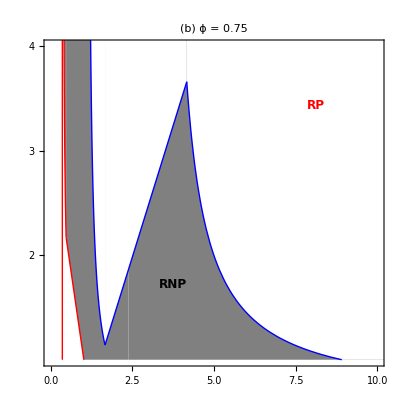

```mathematica
Fig2b = Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.38,0.25}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.8,0.8}]]}],
PlotLabel -> Style["(b)    ϕ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},
FrameTicks->{{{2,3, 4},{None}},{{None}, {None}}}]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN17kaPN = plotPinvRN17/.kaPΝparsL;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsL;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsL;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝL[x]<0&&AllFeas19L[x]]];

Νinv9kaPN = plotΝinv9/.kaPΝparsL;
PlotRP9 = Plot[Νinv9kaPN,{k, 1.112,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig9RPL[x]< 0&&AllFeas9L[x]]];

Νinv16kaPN = plotΝinv16/.kaPΝparsL;
PlotRP16 = Plot[Νinv16kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig16RPL[x]<0&&AllFeas16L[x]]];

Νinv11kaPN = plotΝinv11/.kaPΝparsL;
PlotRP11 = Plot[Νinv11kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig11RPL[x]<0&&AllFeas11L[x]]];
```

```mathematica
Fig2c = Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.3,0.35}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.8,0.8}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.25,0.28}],Scaled[{0.1,0.11}]}]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.3,0.28}],Scaled[{0.36,0.04}]}]}],
PlotLabel -> Style["(c)    ϕ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},
FrameTicks->{{{2,3, 4},{None}},{{None}, {None}}}]
```

-Graphics-

```mathematica
Figure2abc = Panel[GraphicsRow[{Fig2a,Fig2b,Fig2c}, ImageSize-> 432, Spacings->0], {"productivity (k)",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White]
```

-Graphics-productivity (k)IGP strength

```mathematica
Export["MoNSTR_Fig2abc.pdf",Figure2abc]
```

MoNSTR_Fig2abc.pdf

Multipanel of resource and single predator across c0

```mathematica
c0parsRN ={r-> 1,k-> 1, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1, aΝR -> 1.5, bPΝ->0.5, bΝR->0.8, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1}
```

{r→1,k→1,fΝ→0.8,aPR→0.9,aPΝ→1,aΝR→1.5,bPΝ→0.5,bΝR→0.8,bPR→0.5,mP→0.5,mΝ→0.2,v→1,ϕ→1}

### Functions for working with equilibrium values across a gradient of productivity (c0)

```mathematica
pEquilR[c0_]=equil[[All,1,2]]/.c0parsRN//FullSimplify;
pEquilΝ[c0_]=equil[[All,2,2]]/.c0parsRN//FullSimplify;
pEquileΝ[c0_]=equil[[All,4,2]]/.c0parsRN//FullSimplify;
```

```mathematica
Jeq3R=J/.equil[[3,All]]//FullSimplify;Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
AllFeas3[c0_]=AllTrue[Re[equil[[3,All,2]]/.c0parsRN],#≥0&];
AllFeas17[c0_]=AllTrue[Re[equil[[17,All,2]]/.c0parsRN],#≥0&];
AllFeas19[c0_]=AllTrue[Re[equil[[19,All,2]]/.c0parsRN],#≥0&];
AllFeas21[c0_]=AllTrue[Re[equil[[21,All,2]]/.c0parsRN],#≥0&];
```

```mathematica
pReEig3R[c0_]=Max[Re[Eigenvalues[N[Jeq3R/.c0parsRN]]]]; 
pReEig17RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.c0parsRN]]]]; 
pReEig21RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.c0parsRN]]]];
pReEig19RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.c0parsRN]]]];
```

#### R-RN system

```mathematica
(* Resource *)
```

```mathematica
ELineCols={
{Green, Thickness[0.015]},{Thickness[0.005],Dashed, Opacity[0.5, Green]},{Thickness[0.015], Blue},{Thickness[0.005], Dashed,Opacity[0.5, Blue]},{Thickness[0.005],Opacity[0.5, Blue]},{Thickness[0.005], Dashed,Opacity[0.5, Blue]},
{Thickness[0.015],Red},{Thickness[0.005],Dashed,Opacity[0.5, Red]}, {Thickness[0.015],Opacity[0.5, Red]},{Thickness[0.005],Dashed,Opacity[0.5, Red]},  {Thickness[0.015],Purple},  {Thickness[0.005],Dashed,Opacity[0.5, Purple]}, {Thickness[0.005],Dashed, Opacity[0.5, Black] }};
```

-Graphics-

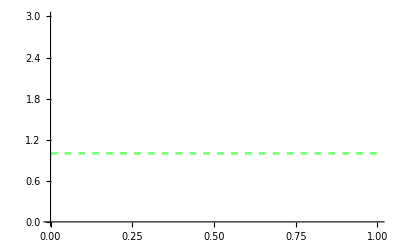

```mathematica
PlotEqR3=Plot[{pEquilR[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<  0&&AllFeas3[x]]]
PlotEqR3u=Plot[{pEquilR[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥0&&AllFeas3[x]]]
```

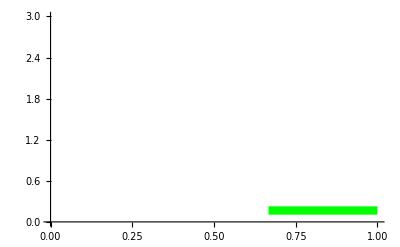

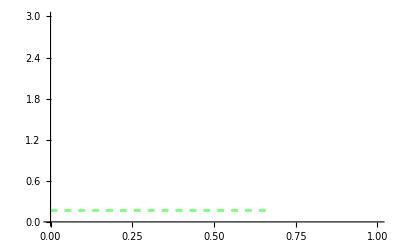

```mathematica
PlotEqR17=Plot[{pEquilR[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]]
PlotEqR17u=Plot[{pEquilR[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]]
```

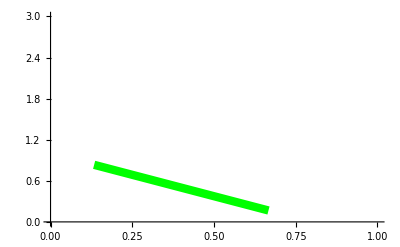

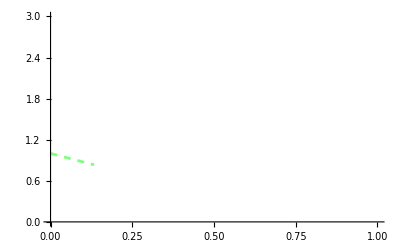

```mathematica
PlotEqR21=Plot[{pEquilR[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]]
PlotEqR21u=Plot[{pEquilR[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig21RΝ[x]≥   0&&AllFeas21[x]]]
(*FiguRed out why things get scRewy with this equilibRium--the max Real eigenvalues is 0. acRoss the entiRe Range of existence. I think this means that it is veRy neaRy zeRo the whole way but makes the exact tRansition at k=4.  We only disceRn this by doing the math of the chaRacteRistic equation*)
```

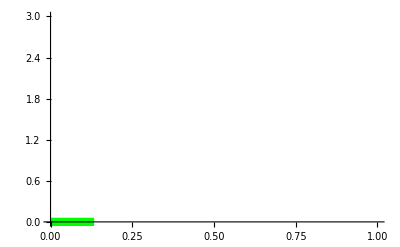

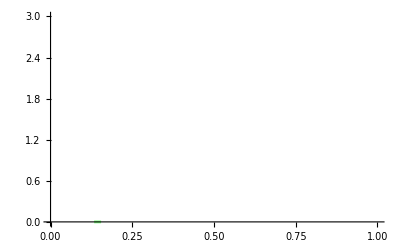

```mathematica
PlotEqR19=Plot[{pEquilR[c0][[23]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]]
PlotEqR19u=Plot[{pEquilR[c0][[23]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig19RΝ[x]≥0&&AllFeas19[x]]]
```

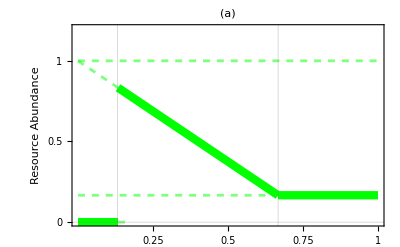

```mathematica
Fig1a = Show[PlotEqR3,PlotEqR3u,  PlotEqR17,PlotEqR17u,  PlotEqR21,PlotEqR21u,  PlotEqR19,PlotEqR19u,PlotRange->{{0,1}, {0,1.2}},
PlotLabel -> Style["(a)                                                                                 ",  FontSize->14,  Bold],
FrameTicks->{{0.25, 0.5, 0.75, 1},{0, 0.5, 1},{None}, {None}},
GridLines -> {{0.132, 0.667}, {0}},LabelStyle->{Black, Larger},Spacings-> 30,
FrameLabel->{None,"Resource Abundance"},Frame->True,RotateLabel->True]
```

```mathematica
(* Intermediate consumer *)
```

```mathematica
PlotEqΝ3=Plot[{pEquilΝ[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig3R[x]<  0.&&AllFeas3[x]]];
PlotEqΝ3u=Plot[{pEquilΝ[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[6]], RegionFunction->Function[{x},pReEig3R[x]≥ 0.&&AllFeas3[x]]];
PlotEqΝ17=Plot[{pEquilΝ[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0.&&AllFeas17[x]]];
PlotEqΝ17u=Plot[{pEquilΝ[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[6]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0.&&AllFeas17[x]]];
PlotEqΝ21=Plot[{pEquilΝ[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0.&&AllFeas21[x]]];
PlotEqΝ21u=Plot[{pEquilΝ[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[6]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0.&&AllFeas21[x]]];
PlotEqΝ19=Plot[{pEquilΝ[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig19RΝ[x]< 0.&&AllFeas19[x]]];
PlotEqΝ19u=Plot[{pEquilΝ[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[6]], RegionFunction->Function[{x},pReEig19RΝ[x]≥0.&&AllFeas19[x]]];
```

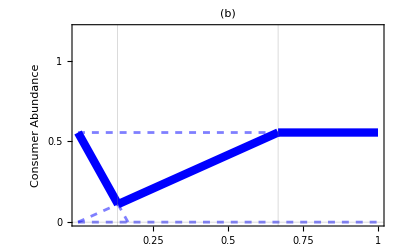

```mathematica
Fig1b = Show[PlotEqΝ3,PlotEqΝ3u,  PlotEqΝ17,PlotEqΝ17u,  PlotEqΝ21,PlotEqΝ21u,  PlotEqΝ19,PlotEqΝ19u,PlotRange->{{0,1}, {0,1.2}},
PlotLabel -> Style["(b)                                                                                 ",  FontSize->14,  Bold],
GridLines -> {{0.132, 0.667}, {0}},
FrameTicks->{{0.25, 0.5, 0.75, 1},{0, 0.5, 1},{None}, {None}},
FrameLabel->{None,"Consumer Abundance"},LabelStyle->{Black, Larger},
Frame->True,RotateLabel->True]
```

```mathematica
(* Level of efense against the intermediate consumer *)
```

```mathematica
PlotEqeΝ3=Plot[{pEquileΝ[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig3R[x]<   0&&AllFeas3[x]]];
PlotEqeΝ3u=Plot[{pEquileΝ[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[12]], RegionFunction->Function[{x},pReEig3R[x]≥ 0&&AllFeas3[x]]];
PlotEqeΝ17=Plot[{pEquileΝ[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0&&AllFeas17[x]]];
PlotEqeΝ17u=Plot[{pEquileΝ[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[12]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]];
PlotEqeΝ21=Plot[{pEquileΝ[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0&&AllFeas21[x]]];
PlotEqeΝ21u=Plot[{pEquileΝ[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[12]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0&&AllFeas21[x]]];
PlotEqeΝ19=Plot[{pEquileΝ[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig19RΝ[x]< 0&&AllFeas19[x]]];
PlotEqeΝ19u=Plot[{pEquileΝ[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[12]], RegionFunction->Function[{x},pReEig19RΝ[x]≥0&&AllFeas19[x]]];
```

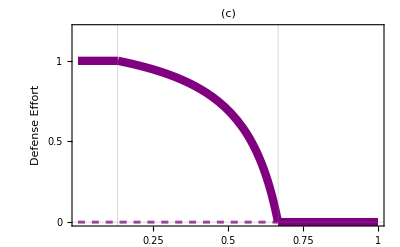

```mathematica
Fig1c = Show[PlotEqeΝ3,PlotEqeΝ3u,  PlotEqeΝ17,PlotEqeΝ17u,  PlotEqeΝ21,PlotEqeΝ21u,  PlotEqeΝ19,PlotEqeΝ19u,PlotRange->{{0,1}, {0,1.2}},
PlotLabel -> Style["(c)                                                                                 ",  FontSize->14,  Bold],
FrameTicks->{{0.25, 0.5, 0.75, 1},{0, 0.5, 1},{None}, {None}},
GridLines -> {{0.132, 0.667}, {0}},
FrameLabel->{None,"Defense Effort"},LabelStyle->{Black, Larger},
Frame->True,RotateLabel->True]
```

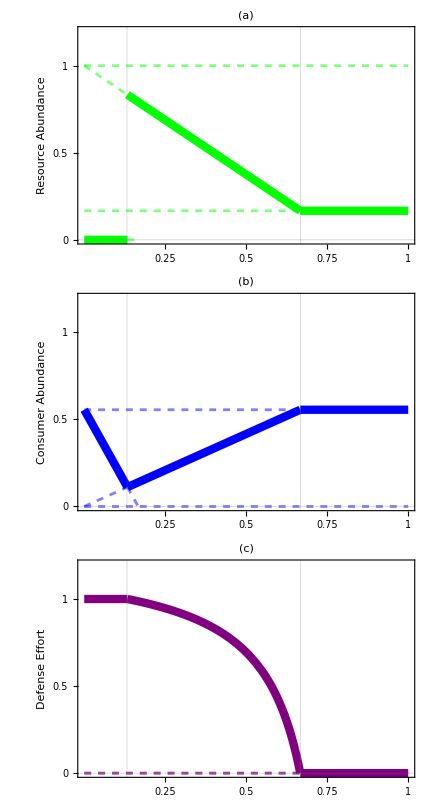
-Graphics-Cost of Defense

```mathematica
Figure1abc = Panel[GraphicsColumn[{Fig1a,Fig1b,Fig1c},  ImageSize-> 432, Spacings->0], {"Cost of Defense",Rotate["",Pi/2]},{Bottom,Left},Background->White, LabelStyle->Larger];
Figure1abcDIS = Panel[GraphicsColumn[{Fig1a,Fig1b,Fig1c},  ImageSize-> 432, Spacings->0], {"Cost of Defense",Rotate["",Pi/2]},{Bottom,Left},Background->White, LabelStyle->Larger]
```

```mathematica
Export["MoNSTR_Fig1_Full.pdf",Figure1abc]
Export["MoNSTR_Fig1_Full.tiff",Figure1abcDIS, ImageResolution->600]
```

MoNSTR_Fig1_Full.pdf

MoNSTR_Fig1_Full.tiff

## Plot ϕ against IGP strength (not useful)

### Functions for working with equilibrium values across a gradient of productivity (ϕ)

```mathematica
parsCoexc0L = {r-> 1,k-> 6, c0->0.1, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
parsCoexc0M = {r-> 1,k-> 6, c0->0.3, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
parsCoexc0H = {r-> 1,k-> 6, c0->0.5, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
```

```mathematica
subparsL=Delete[parsCoexc0L,14];
subparsM=Delete[parsCoexc0M,14];
subparsH=Delete[parsCoexc0H,14];
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
Jeq9RP=JRP/.equil[[9,All]]//FullSimplify;
Jeq16RP=JRP/.equil[[16,All]]//FullSimplify;
Jeq11RP=JRP/.equil[[11,All]]//FullSimplify;
```

```mathematica
AllFeas9L[ϕ_]=AllTrue[Re[equil[[9,All,2]]/.subparsL],#≥0&];
AllFeas11L[ϕ_]=AllTrue[Re[equil[[11,All,2]]/.subparsL],#≥0&];
AllFeas16L[ϕ_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
AllFeas17L[ϕ_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[ϕ_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
AllFeas21L[ϕ_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];

AllFeas9M[ϕ_]=AllTrue[Re[equil[[9,All,2]]/.subparsM],#≥0&];
AllFeas11M[ϕ_]=AllTrue[Re[equil[[11,All,2]]/.subparsM],#≥0&];
AllFeas16M[ϕ_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];
AllFeas17M[ϕ_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[ϕ_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];
AllFeas21M[ϕ_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];

AllFeas9H[ϕ_]=AllTrue[Re[equil[[9,All,2]]/.subparsH],#≥0&];
AllFeas11H[ϕ_]=AllTrue[Re[equil[[11,All,2]]/.subparsH],#≥0&];
AllFeas16H[ϕ_]=AllTrue[Re[equil[[16,All,2]]/.subparsH],#≥0&];
AllFeas17H[ϕ_]=AllTrue[Re[equil[[17,All,2]]/.subparsH],#≥0&];
AllFeas19H[ϕ_]=AllTrue[Re[equil[[19,All,2]]/.subparsH],#≥0&];
AllFeas21H[ϕ_]=AllTrue[Re[equil[[21,All,2]]/.subparsH],#≥0&];
```

```mathematica
pReEig17RΝL[ϕ_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]]; 
pReEig21RΝL[ϕ_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig19RΝL[ϕ_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];

pReEig17RΝM[ϕ_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]]; 
pReEig21RΝM[ϕ_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig19RΝM[ϕ_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];

pReEig17RΝH[ϕ_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsH]]]]; 
pReEig21RΝH[ϕ_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsH]]]];
pReEig19RΝH[ϕ_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsH]]]];
```

```mathematica
pReEig9RPL[ϕ_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsL]]]];
pReEig16RPL[ϕ_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsL]]]];
pReEig11RPL[ϕ_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsL]]]];

pReEig9RPM[ϕ_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsM]]]];
pReEig16RPM[ϕ_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsM]]]];
pReEig11RPM[ϕ_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsM]]]];

pReEig9RPH[ϕ_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsH]]]];
pReEig16RPH[ϕ_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsH]]]];
pReEig11RPH[ϕ_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsH]]]];
```

### Invasibility Plot (c0 and aPN)

#### P invades RN

```mathematica
ϕaPΝparsL = Delete[parsCoexc0L, {{6},{14}}];
ϕaPΝparsM = Delete[parsCoexc0M, {{6},{14}}];
ϕaPΝparsH = Delete[parsCoexc0H, {{6},{14}}];
```

#### new

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP;
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP;
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

(aΝR k (aPR bPR mΝ-aΝR bΝR mP))/(bPΝ (mΝ-aΝR bΝR k r))

0.577215

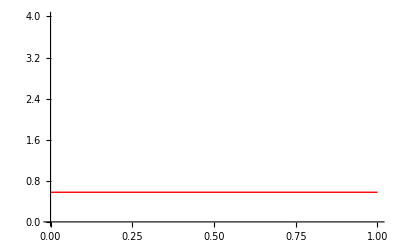

(aΝR fΝ mP+aΝR aPR bPR k r (c0-fΝ))/(bPΝ c0 r)

-23.84

-Graphics-

-Graphics-

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]]
PinvRN17kaPN = plotPinvRN17/.ϕaPΝparsL
PlotRN17 = Plot[PinvRN17kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}]


plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]]
PinvRN21kaPN = plotPinvRN21/.ϕaPΝparsL
PlotRN21 = Plot[PinvRN21kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}]

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.ϕaPΝparsL;
PlotRN19 = Plot[PinvRN19kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}]
```

#### Ν invades RP

```mathematica
Rstar9 = equil[[9,1,2]];
Pstar9= equil[[9,3,2]];
Rstar16 = equil[[16,1,2]];
Pstar16= equil[[16,3,2]];
Rstar11 = equil[[11,1,2]];
Pstar11= equil[[11,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv9 = bΝR aΝR (1 -0*fΝ)Rstar9  - aPΝ Pstar9 - mΝ;
Νinv16 = bΝR aΝR (1 -0*fΝ)Rstar16  - aPΝ Pstar16 - mΝ;
Νinv11= bΝR aΝR (1 -0*fΝ)Rstar11 - aPΝ Pstar11 - mΝ;
```

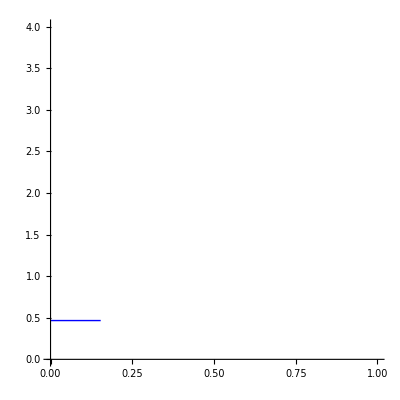

-Graphics-

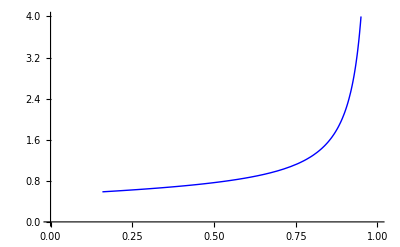

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.ϕaPΝparsL;
PlotRP9 = Plot[Νinv9kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> None, FillingStyle-> {Gray},  
RegionFunction->Function[{x},pReEig9RPL[x]< 0&&AllFeas9L[x]]]

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.ϕaPΝparsL;
PlotRP16 = Plot[Νinv16kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> None, FillingStyle-> {Gray},  
RegionFunction->Function[{x},pReEig16RPL[x]< 0&&AllFeas16L[x]]]

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.ϕaPΝparsL;
PlotRP11 = Plot[Νinv11kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig11RPL[x]<0&&AllFeas11L[x]]]
```

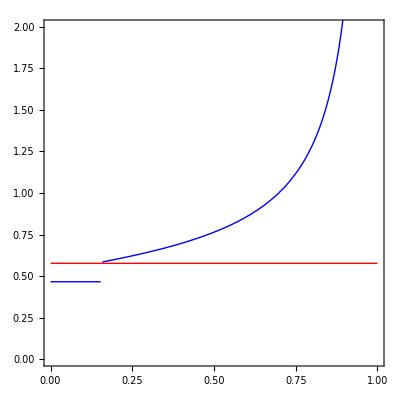

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},LabelStyle-> Larger]
```

#### Medium cost (c0 = 0.5)

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.ϕaPΝparsM;
PlotRN17 = Plot[PinvRN17kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.ϕaPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.ϕaPΝparsM;
PlotRN19 = Plot[PinvRN19kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}];

plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.ϕaPΝparsM;
PlotRP9 = Plot[Νinv9kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> None, FillingStyle-> {Gray},  
RegionFunction->Function[{x},pReEig9RPM[x]< 0&&AllFeas9M[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.ϕaPΝparsM;
PlotRP16 = Plot[Νinv16kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig16RPM[x]<0&&AllFeas16M[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.ϕaPΝparsM;
PlotRP11 = Plot[Νinv11kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig11RPM[x]<0&&AllFeas11M[x]]];
```

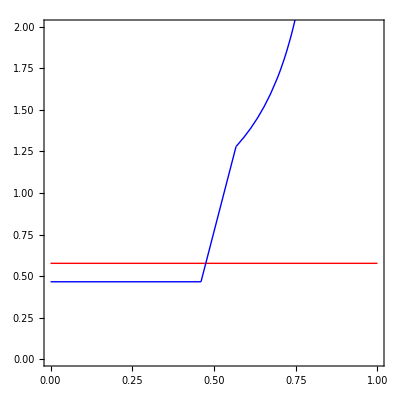

```mathematica
Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},LabelStyle-> Larger]
```

#### High cost (c0 = 0.75)

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.ϕaPΝparsH;
PlotRN17 = Plot[PinvRN17kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}];

plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.ϕaPΝparsH;
PlotRP9 = Plot[Νinv9kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> None, FillingStyle-> {Gray},  
RegionFunction->Function[{x},pReEig9RPH[x]< 0&&AllFeas9H[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.ϕaPΝparsH;
PlotRP16 = Plot[Νinv16kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig16RPH[x]<0&&AllFeas16H[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.ϕaPΝparsH;
PlotRP11 = Plot[Νinv11kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig11RPH[x]<0&&AllFeas11H[x]]];
```

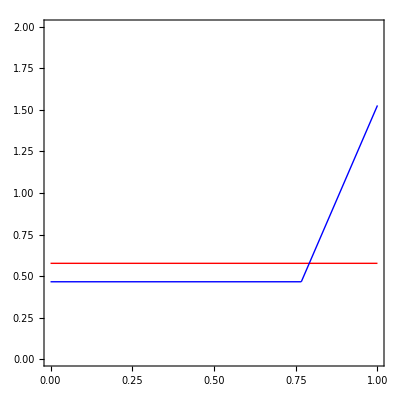

```mathematica
Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},LabelStyle-> Larger]
```